# Feynman’s Particles

Richard Feynman, one of the most influential physicists of our time, is very well known for his ability to communicate difficult physical concepts to people new to physics, perhaps even to experts. In one of his famous lectures (watch here), he explains the bizarreness of quantum mechanics by picturing a thought experiments where classical particles, such as bullets fired from a shaky machine gun, are pointed at a wall with two slits beyond which another wall is placed to catch them. He explains the bullets are expected to create a fuzzy print of the slits on the wall if they behave classically. However, if this machine gun was operating in the quantum realm, one would see an interference pattern instead, contrary to common intuition. Feynman also received a Nobel prize for reformulating quantum mechanics with principle of least action where each particles takes a random path from point A to point B which its probability (amplitude) is related to the associated action to the taken path. In this essay, I would like to go back to Feynman’s machine gun and replace the straight flying bullets and replace them with  randomly flying particles with some momentum directed at the double slits. In this computational essay, I am attempting to replace his modified thought experiment with what I like to call computational thought experiment.

First, we must develop a mechanism for detecting if the particle crosses the chamber or slit walls. One way to do this is to obtain the common the region of intersection using  RegionIntersection. If there is an intersection between the two lines, RegionMeasure would return 1, and if the lines do not intersect, it will return 0.

```mathematica
lineCrossRegionMeasure[line1_,line2_]:=RegionIntersection[Region[Line@line1],Region[Line@line2]]//RegionMeasure

Animate[
	Block[{line1, line2, line3},
		line1 = {{2, 3}, {5, 3}};
		line2 = {{3, 2}, {5, 6}};
		line3 = line1 + {{0, 0}, {-a, +a}};
		Grid[{
			{Graphics[{{Red, Line[line3]}, {Blue, Line[line2]}}, ImageSize -> Tiny]},
			{"lineCrossRegionMeasure = ", lineCrossRegionMeasure[line3, line2]}
		}]
	]
	,
	{a, 0.2, 1.5}
]
```

```mathematica
ClearAll["Global`*"]
(* Given the end points of two lines, do they cross *)
linePointCrossQ[A1_,B1_,A2_,B2_]:=Quiet[Reduce[Exists[{u,v},A1+u*(B1-A1)==A2+v*(B2-A2)&&0≤u≤1&&0≤v≤1]]]

(* Shorthand for linePointCrossQ, using lines rather than endpoints *)
lineCrossQ[line1_,line2_]:=linePointCrossQ[line1⟦1⟧,line1⟦2⟧,line2⟦1⟧,line2⟦2⟧]

(* Using RegionMeasure on RegionIntersection of two given lines *)
lineCrossRegionMeasure[line1_,line2_]:=RegionIntersection[Region[Line@line1],Region[Line@line2]]//RegionMeasure
```

```mathematica
Animate[
	Block[{line1, line2, line3},
		line1 = {{2, 3}, {5, 3}};
		line2 = {{3, 2}, {5, 6}};
		line3 = line1 + {{0, 0}, {-a, +a}};
		Grid[{
			{Graphics[{{Red, Line[line3]}, {Blue, Line[line2]}}, ImageSize -> Tiny]},
			{"lineCrossQ             = ", lineCrossQ[line3, line2]},
			{"lineCrossRegionMeasure = ", lineCrossRegionMeasure[line3, line2]}
		}]
	]
	,
	{a, 0.2, 1.5}
]
```

Next, we construct the chamber and slit boundaries and place the source between the wall and the slit.

```mathematica
chamber[
	chamberLength_: 25, 
	chamberHalfWidth_: 10, 
	slitScreenDistance_: 20, 
	slitWidth_: 1, 
	slitHalfSeparation_: 1] := 
	
	Module[{},	
		w1 = {0, +chamberHalfWidth};
		w2 = {0, -chamberHalfWidth};
		w3 = {chamberLength, -chamberHalfWidth};
		w4 = {chamberLength, +chamberHalfWidth};
		
		l1 = {w1, w2};
		l2 = {w2, w3};
		l3 = {w3, w4};
		screen = l3;
		l4 = {w4, w1};
		
		bx = chamberLength - slitScreenDistance;
		b1 = {bx, -chamberHalfWidth};
		b2 = {bx, -(slitHalfSeparation+slitWidth)};
		l5 = {b1, b2};
		b3 = {bx, -slitHalfSeparation};
		b4 = {bx, +slitHalfSeparation};
		l6 = {b3, b4};
		b5 = {bx, +(slitHalfSeparation+slitWidth)};
		b6 = {bx, +chamberHalfWidth};
		l7 = {b5, b6};
		borders = {l1, l2, (* l3 is screen *) l4, l5, l6, l7, screen};
		borders
	]
```

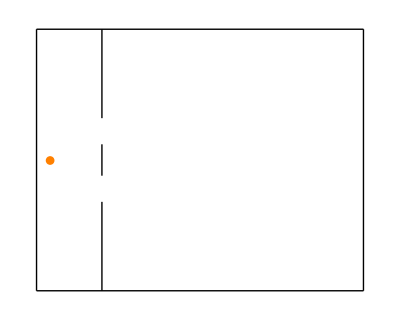

```mathematica
sourcePosition = {1.,0.};
chamberLength=25;
chamberHalfWidth=10;
slitScreenDistance=20;
slitWidth=2;
slitHalfSeparation=1.2;

borders=chamber[chamberLength,chamberHalfWidth,slitScreenDistance,slitWidth,slitHalfSeparation];
Graphics[(Line/@borders)~Join~{Orange, Disk[sourcePosition, First[sourcePosition]/3]}]
```

```mathematica
walk[borders_, sourcePosition_: {0.1, 0.1}, maxNumSteps_: 500] := 
	Module[{path = {sourcePosition}},
		Do[
			r1 = Last[path];
			δx = RandomReal[{-1.0, +2.5} / 10];
			δy = RandomReal[{-1.0, +1.0} / 5];
			r2 = r1 + {δx, δy};
			AppendTo[path, r2];
			If[MemberQ[lineCrossQ[{r1, r2}, #]& /@ borders, True], Break[]]
			,
			{i, maxNumSteps}
		];
	
		path
	]

chamberWalk[borders_, sourcePosition_: {0.1, 0.1}, maxNumWalks_: 10, maxNumSteps_: 500] := 
	Module[{goodPaths={},screenLine = Last[borders]},
		Do[
			path = walk[borders, sourcePosition, maxNumSteps];
			(* Does it colide with the screen? *)
			isGoodMeasurement = lineCrossQ[{path⟦-2⟧, path⟦-1⟧}, screenLine];
			If[
				isGoodMeasurement,
				AppendTo[goodPaths, path]
			];
			,
			{i, maxNumWalks}
		];
		goodPaths
	]
```

```mathematica
(*$KernelCount
LaunchKernels[2]*)
```

24

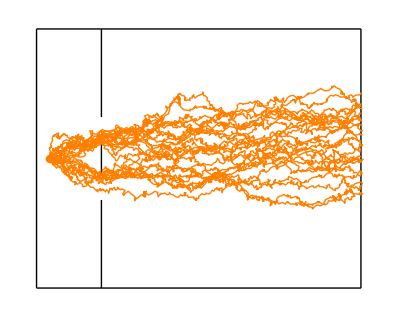

```mathematica
goodPaths = chamberWalk[borders,sourcePosition,100,500];

Length@goodPaths
Graphics[
	(Line /@ borders)~Join~
	{Orange, Disk[sourcePosition, First[sourcePosition]/3]}~Join~
	{Line/@goodPaths}
]
```